```mathematica
Solve[e==1/2(px^2+py^2+x^2+1/16 y^2)+x^2 y/16+1/3 y^3,px]
```

{{px→-(√(96 e-48 py^2-48 x^2-6 x^2 y-3 y^2-32 y^3))/(4 √3)},{px→(√(96 e-48 py^2-48 x^2-6 x^2 y-3 y^2-32 y^3))/(4 √3)}}

```mathematica
(√(96 e-48 py^2-48 x^2-6 x^2 y-3 y^2-32 y^3))/(4 √3)
```

(√(96 e-48 py^2-48 x^2-6 x^2 y-3 y^2-32 y^3))/(4 √3)

```mathematica
Simplify[(√(96 e-48 py^2-48 x^2-6 x^2 y-3 y^2-32 y^3))/(4 √3)]
```

1/4 √(32 e-16 py^2-16 x^2-2 x^2 y-y^2-(32 y^3)/3)

```mathematica
D[1/2(x^2+1/16 y^2)+x^2 y/16+1/3 y^3,x]
```

x+(x y)/8

```mathematica
D[1/2(x^2+1/16 y^2)+x^2 y/16+1/3 y^3,y]
```

x^2/16+y/16+y^2

```mathematica
Series[1/2(x^2+y^2)+x^2 y+1/3 y^3,{}]
```

```mathematica
Manipulate[Plot[{2L p-p^2(1-E^(-L/p))},{L,0,500}],{p,40,50}]
```

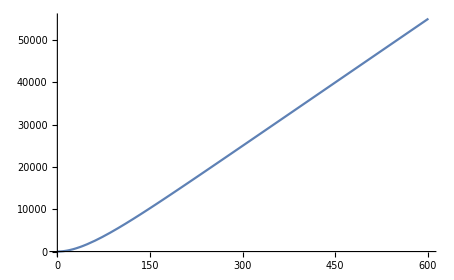

```mathematica
g=Plot[{100 L -2*50^2(1-E^(-L/50))},{L,0,601}]
```

```mathematica
{75,3673.9178220182553},{150,10596.997619869811},{300,25748.024898621443},{60,52422.509038839824}
```

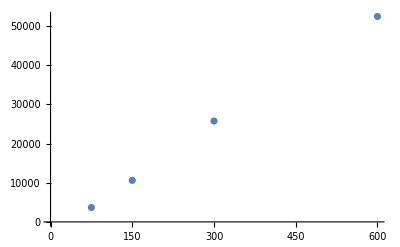

```mathematica
f=ListPlot[{{75,3673.9178220182553},{150,10596.997619869811},{300,25748.024898621443},{600,52422.509038839824}}]
```

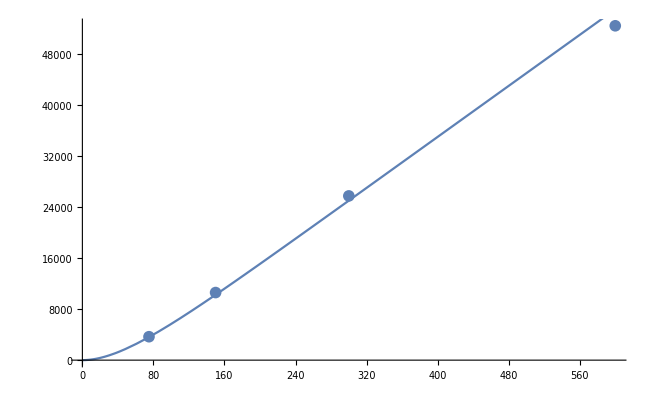

```mathematica
Show[f,g]
```

```mathematica
Log[10]+Log[50]-Log[500]
```

Log[10]+Log[50]-Log[500]

```mathematica
N[Log[10]+Log[50]-Log[500]]
```

0.

```mathematica
FindFit[{{75,3673.9178220182553},{150,10596.997619869811},{300,25748.024898621443},{600,52422.509038839824}},2*P L -2*P^2(1-E^(-L/P)),P,L]
```

{P→48.117}

```mathematica
5.5*150
```

825.

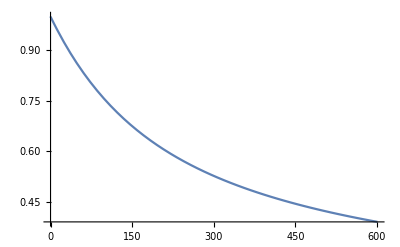

```mathematica
Plot[{Sqrt[100 L -2*50^2(1-E^(-L/50))]/L},{L,0,601}]
```

```mathematica
FindFit[Sample,2*P,L,-2*P^2(1-E^(-L/P)),P,L]
```